```mathematica
NS["fmri_alzheimer"]
```

```mathematica
(* Load data given by Claudia *)
datafull=<<"claudia_test5_mean_short.txt";
(* Check how many parameters, health groups, individuals *)
{Length[T@datafull],Length[datafull],Length[T@datafull[[1]]]}
```

{6,3,13}

```mathematica
(* Order of health groups and parameters of the data *)
{health,parnames}=(<<"claudia_test5_mean_names.txt")
```

{{H,C,A},{graph weights,shortest path,cluster coefficient,degree,modularity,number of nodes}}

```mathematica
(* Empirical means and standard deviations *)
meansall=Table[Mean@T@datafull[[i]],{i,3}]//N
```

{{0.627358,1.68921,0.64025,156.341,0.056081,249.615},{0.653689,1.60256,0.663035,147.878,0.0461562,229.667},{0.657526,1.607,0.667931,146.964,0.0409293,224.923}}

```mathematica
stdall=Table[Std@T@datafull[[i]],{i,3}]//N
```

{{0.0923868,0.286423,0.0820397,27.9338,0.0345552,19.2215},{0.085302,0.268161,0.075857,14.9414,0.0303107,26.1831},{0.0809806,0.218788,0.0792804,24.7297,0.01745,30.8482}}

```mathematica
(* Logarithm of predictive distribution {P(x|H,data), P(x|C,data), P(x|A,data)} 
it also calculates and stores expectations and covariances *)
ClearAll[means,istdmatrix,num];lntstudent[x_,data_]:=Module[{health=Length@data,d=Length[T@data],n,dscatter,idscatter},Table[(* number individuals *) n[i]=Length[T[data[[i]]]];num[i]=n[i];
means[i]=Mean@T@data[[i]];
(* scatter matrix with numerical factor *)dscatter[i]=(n[i]+1)/n[i]*(data[[i]]-means[i]).T[data[[i]]-means[i]]; 
idscatter[i]=Inverse[dscatter[i]];
istdmatrix[i]=Inverse[dscatter[i]/(n[i]-1-d)];

(* logarithm of t-distribution *)
Log[Gamma[(n[i]+1)/2]]-Log[Gamma[(n[i]+1-d)/2]]-Log[Det[dscatter[i]*Pi]]/2-(n[i]+1)*Log[1+(x-means[i]).idscatter[i].(x-means[i])]/2,

{i,health}]]
```

```mathematica
(* Distributions with the actual data. 
It won't actually be used *)

pdfall[x1_,x2_,x3_,x4_,x5_,x6_]=Simplify@Exp[lntstudent[{x1,x2,x3,x4,x5,x6},datafull]]
```

{2.05112×10^-25/(0.692326+1. x1^2+0.0116487 x2^2-0.863219 x3+1.16201 x3^2+0.00659825 x4-0.00683472 x3 x4+0.0000202038 x4^2+0.230207 x5-0.74349 x3 x5+0.00183247 x4 x5+0.154646 x5^2+x2 (-0.0706737-0.0825175 x3+0.000076665 x4+0.017656 x5-0.0000460586 x6)+x1 (-0.949312+0.131778 x2-0.924495 x3-0.0027433 x4+0.37627 x5+0.00188967 x6)-0.00465231 x6+0.00482699 x3 x6-0.0000282472 x4 x6-0.00129761 x5 x6+9.90141×10^-6 x6^2)^7,2996.89/(6918.24+36938.1 x1^2+941.332 x2^2+4907.79 x3+28490.4 x3^2-13.8957 x4+15.509 x3 x4+0.0319991 x4^2+1824.62 x5-12139.1 x3 x5-2.56106 x4 x5+3034.05 x5^2+x2 (-4949.82-547.358 x3+7.18665 x4-875.516 x5-5.72682 x6)+11.5295 x6-14.6896 x3 x6-0.0464521 x4 x6+2.53595 x5 x6+0.0175601 x6^2+x1 (-15043.+3959.97 x2-61451.7 x3-10.0684 x4+10927.7 x5+9.29181 x6))^(13/2),8.08295×10^-25/(0.168537+1. x1^2+0.0205358 x2^2+0.311791 x3+0.621728 x3^2+0.000574949 x4-0.00114112 x3 x4+6.06359×10^-6 x4^2-0.0380293 x5-0.200824 x3 x5-0.000429594 x4 x5+0.163493 x5^2+x2 (-0.0778042-0.149929 x3+0.000363134 x4-0.019808 x5-0.000229761 x6)+x1 (-0.64791+0.168915 x2-1.37556 x3-0.000746359 x4+0.291954 x5+0.000346467 x6)-0.000341834 x6+0.000795783 x3 x6-7.42583×10^-6 x4 x6+0.000274676 x5 x6+2.29369×10^-6 x6^2)^7}

```mathematica
(* Normalization check *)NIntegrate[Evaluate[pdfall[x1,x2,x3,x4,x5,x6][[1]]]*Boole[({x1,x2,x3,x4,x5,x6}-means[1]).istdmatrix[1].({x1,x2,x3,x4,x5,x6}-means[1])<8],{x1,-Infinity,Infinity},{x2,-Infinity,Infinity},{x3,-Infinity,Infinity},{x4,-Infinity,Infinity},{x5,-Infinity,Infinity},{x6,-Infinity,Infinity},PrecisionGoal->1,AccuracyGoal->+Infinity]
```

0.811004

```mathematica
(* Separately: Healthy, Alzheimer, Cognit. impaired *)
pdfh[x1_,x2_,x3_,x4_,x5_,x6_]=pdfall[x1,x2,x3,x4,x5,x6][[1]];
pdfa[x1_,x2_,x3_,x4_,x5_,x6_]=pdfall[x1,x2,x3,x4,x5,x6][[3]];
pdfc[x1_,x2_,x3_,x4_,x5_,x6_]=pdfall[x1,x2,x3,x4,x5,x6][[2]];
```

```mathematica
(* The three distributions are 6-dimensional. To visualize them, in this 6D space we choose a 2D section that passes through their centres. Then we plot the curves of 1 and 2 standard deviations. *)

(* Affine-combination coefficients for the contour plot *)
ac[1,x_,y_]=-x-y/Sqrt[3]+1;ac[3,x_,y_]=x-y/Sqrt[3];ac[2,x_,y_]=Simplify[1-ac[1,x,y]-ac[3,x,y]];
seq=FS@Table[Sum[ac[ii,x,y]*meansall[[ii,jj]],{ii,3}],{jj,6}]
```

{0.627358+0.0301678 x+0.0129869 y,1.68921-0.0822138 x-0.0525965 y,0.64025+0.0276808 x+0.010328 y,156.341-9.37726 x-4.35885 y,0.056081-0.0151517 x-0.00271238 y,249.615-24.6923 x-8.77868 y}

```mathematica
(* We plot the three separately and then join them *)
colours={green,yellow,red};Do[cont[i]=ContourPlot[(seq-means[i]).istdmatrix[i].(seq-means[i]),{x,-2,3},{y,-2,3},Contours->{1,2},ContourShading->None,ContourStyle->{Directive[Opacity[0.75],Thick,colours[[i]]],Directive[Dashed,Opacity[0.75],Medium,colours[[i]]]},FrameTicks->None,FrameLabel->Evaluate[myaxes[{"affine combination of 6 parameters","affine combination of 6 parameters"}]],PlotLegends->If[i==3,mylegendsc[{green,red,yellow,White,{Gray,Thick},{Gray,Dashed,Medium}},{"H","A","MCI"," ", "1 std","2 std"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,{1,3,2}}];
centres=Graphics[{{green,PointSize[Large],Point[{0,0}]},{red,PointSize[Large],Point[{1,0}]},{yellow,PointSize[Large],Point[{1/2,Sqrt[3]/2}]}}];
```

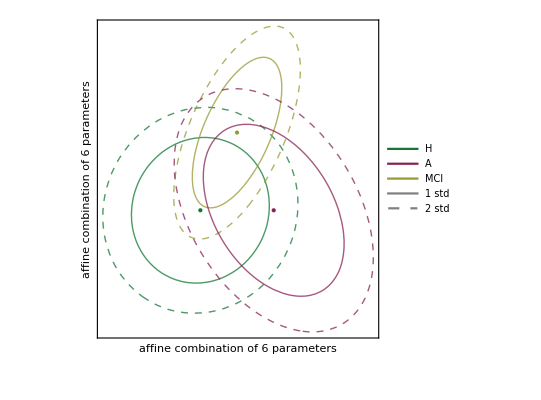

```mathematica
Show[Join[Array[cont,3],{centres}]]
```

```mathematica
(* export to pdf file *)
expdf["stds_6_params"]
```

../work/stds_6_params.pdf

```mathematica
(* These are some scripts just to copy the data on the latex file *)Grid[Table[{"$"<>ToString[i+13*2]<>"$ & C & $("<>ToString[T[datafull[[2]]][[i]]]<>")$ \\\\"},{i,12} ]]
```

$27$ & C & $({0.575399, 1.84898, 0.596428, 140.973, 0.080927, 246})$ \\
$28$ & C & $({0.687646, 1.48628, 0.691763, 144.406, 0.04448, 211})$ \\
$29$ & C & $({0.576417, 1.81166, 0.583679, 129.694, 0.051219, 226})$ \\
$30$ & C & $({0.669721, 1.5166, 0.672916, 129.926, 0.032039, 195})$ \\
$31$ & C & $({0.736418, 1.36799, 0.73886, 145.074, 0.022411, 198})$ \\
$32$ & C & $({0.743739, 1.35582, 0.746371, 174.035, 0.024474, 235})$ \\
$33$ & C & $({0.664138, 1.55512, 0.673374, 156.736, 0.034872, 237})$ \\
$34$ & C & $({0.614609, 1.69503, 0.624112, 132.756, 0.045331, 217})$ \\
$35$ & C & $({0.439049, 2.31677, 0.478943, 131.715, 0.13096, 301})$ \\
$36$ & C & $({0.728062, 1.38382, 0.730246, 165.998, 0.021884, 229})$ \\
$37$ & C & $({0.719449, 1.4011, 0.721807, 161.157, 0.020809, 225})$ \\
$38$ & C & $({0.689622, 1.49152, 0.697921, 162.061, 0.044468, 236})$ \\

```mathematica
Table[If[i<=j,ToString[(datafull[[1]].T@datafull[[1]])[[i,j]]/Length[T@datafull[[1]]]],""],{i,6},{j,6}]//MF
```

(0.402114 | 1.03346 | 0.409205 | 100.371 | 0.0324141 | 156.968
 | 2.93548 | 1.05846 | 256.904 | 0.103465 | 420.29
 |  | 0.416651 | 102.093 | 0.0335846 | 160.097
 |  |  | 25222.8 | 7.99839 | 39366.2
 |  |  |  | 0.00433914 | 13.8298
 |  |  |  |  | 62677.3)

```mathematica
hh=2;Grid[
Table[
If[i≤j,ToString[(datafull[[hh]].T@datafull[[hh]])[[i,j]]/Length@T[datafull[[hh]]]],""]<>If[j<6," & "," \\\\"],{i,6},{j,6}]]
```

0.434586 &  | 1.0248 &  | 0.439879 &  | 97.5448 &  | 0.0277439 &  | 148.531 \\
 &  | 2.6401 &  | 1.04242 &  | 234.405 &  | 0.0817666 &  | 373.415 \\
 &  |  &  | 0.44537 &  | 98.8598 &  | 0.0284874 &  | 150.919 \\
 &  |  &  |  &  | 22091. &  | 6.58946 &  | 33961.6 \\
 &  |  &  |  &  |  &  | 0.00304913 &  | 11.2511 \\
 &  |  &  |  &  |  &  |  &  | 53432.3 \\

```mathematica
names
```

```mathematica
datafull[[1,1]]
```

{0.555869,0.525715,0.612931,0.578456,0.453708,0.678076,0.561081,0.736883,0.561073,0.694201,0.72678,0.706357,0.764527}

```mathematica
means[2]//N
```

{0.653689,1.60256,0.663035,147.878,0.0461562,229.667}

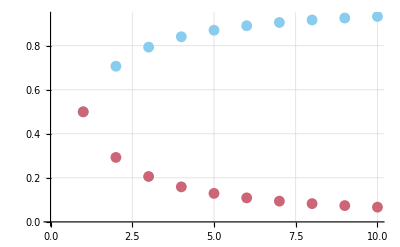

```mathematica
ListPlot[Evaluate@T@Table[{{n,2^(-1/n)},{n,1-2^(-1/n)}},{n,10}],GridLines->Auto]
```

```mathematica
{2^(-1/6),1-2^(-1/6)}//N
```

{0.890899,0.109101}

```mathematica
Solve[0.99^n==1/10,n]
```

{{n→229.105}}

```mathematica
(* error of maximum-likelihood *)
(13+1)/(13-1-6)//N
```

2.33333